# Initial conditions

```mathematica
(*we keep the same values for unrescaled quantities as the numerical solution notebook for matching*)
```

```mathematica
(*Keep m1 > m2. Set Rinit and Pinit so that you start at the point of closest distance. Keep PN parameter small: ϵ ->0, P ->0, 1/R -> 0,  spins/(orb. ang. momentum) -> 0*)

m1=5/2;m2=1;G=1 ;
ϵ= 3/1000; 
tfin =   (*500/ϵ *)  15000  ;
precisionGoal=Automatic (* 50*)  ;
spinSuppressFac = ϵ^(1/2);    c = 1/spinSuppressFac   ;    kGoldstein = G M μ ;  M = m1+m2 ;  μ = m1 m2/M ;ν=μ/M; spinScalingFactor = G M μ ;
Rinit=2{ 1,1,1};
Pinit=1{1/2,-1/2,1/3};
S1init={0,1,1}/spinScalingFactor spinSuppressFac ;         
S2init={1,-3/10,0}/spinScalingFactor spinSuppressFac ;
(*These spin numbers (times spinSuppressFac) entered by user are unscaled quantities. But S1init and S2init are scaled (reduced) spins*)
S1ninit = Norm[S1init];
S2ninit = Norm[S2init];
rinit=Rinit/(G M)     ;     pinit=Pinit/μ ;
Linit=Cross[rinit,pinit] ;     Lninit = Norm[Linit] ;
δ1=2 m1 m2/M^2 (1+3/4 m2/m1)  ;δ2=2 m2 m1/M^2 (1+3/4 m1/m2) ;     rminit = Norm[rinit];
SeffdLinit =   Linit.(δ1  S1init  +  δ2 S2init)  ;
Hinit = Norm[pinit]^2/2 - 1/rminit + ϵ/rminit^3 SeffdLinit + (ϵ-1/8(1-3 ν)Norm[pinit]^4-ϵ/2 1/rminit((3+ν)Norm[pinit]^2+ ν ((rinit/rminit).pinit)^2)+ ϵ/(2 rminit^2))  ; 
m1N =m1; m2N=m2;

(*Prepare  a sign function for later use in solution*)

If [ δ2/(c^2 Norm[rinit]^3 S1ninit Lninit)Linit.Cross[S1init, S2init]   > 0, sign =1, sign =-1 ] ;
```

```mathematica
Jvec= Linit + S1init + S2init  ;  J = Norm[Jvec] ;

sphericalAngles[V_]:=Module[{polarAngJ,azimuthAngJ},
polarAngJ = ToSphericalCoordinates[V][[2]];
azimuthAngJ =  ToSphericalCoordinates[V][[3]];
Return[{polarAngJ,azimuthAngJ}] ; ];

vectorComponents[{V_, θ_, ϕ_}]:=Module[{Vx,Vy,Vz},
Vz = V Cos[θ];
Vx=V Sin[θ]Cos[ϕ];  
Vy=V Sin[θ]Sin[ϕ];
Return[{Vx, Vy, Vz}] ; ];

{ξ2, ξ1}=sphericalAngles[Jvec]+{0,π/2};
EulMat ={ {Cos[ξ1], Sin[ξ1],0},{-Sin[ξ1]Cos[ξ2], Cos[ξ1]Cos[ξ2], Sin[ξ2]},{Sin[ξ1]Sin[ξ2], -Cos[ξ1]Sin[ξ2], Cos[ξ2]}}      ;
  (* Frame A := the one in which the above components are given.

Euler matrix which when multiplies with a column containing components in Frame A yields components in the inertial frame whose z-axis is along J vector (total angular momentum).

Gives components: Basic frame --> J-vector centered frame
*)
```

# Un-rescaled/rescaled quantities

```mathematica
R = {Rx, Ry,Rz} ; P ={Px,Py,Pz};
S1= {S1x, S1y,S1z} ;    S2= {S2x, S2y,S2z} ;
S1n = Norm[S1init] ;     S2n = Norm[S2init] ;

Seff= (δ1 S1+ δ2 S2);
r=R/(G M);       p=P/μ;
L=Cross[r,p] ;
Ln=Norm[Linit] ;
Jn=Norm[Linit+S1init+S2init];
SeffL= Seff.L ;


(*Evaluating σ1 and σ2*)
{Rx,Ry,Rz} = Rinit  ;
{Px,Py,Pz}=Pinit  ;
{S1x,S1y,S1z} = S1init ; 
{S2x,S2y,S2z} = S2init  ;

σ1=(S1.S2)/(S1n S2n) -Ln/S2n(δ1-δ2)/δ2(S1.L)/(Ln S1n) ;   (*σ1=Cos γ -L/S2(Q1-Q2)/Q2 Cos κ1 *)
σ2= (S2.L)/(Ln S2n) + (δ1 S1n)/(δ2 S2n)(S1.L)/(Ln S1n) ;           (*σ2= Cos κ2 +(Q1 S1)/(Q2 S2) Cos κ1*)
Clear[Rx, Ry, Rz, Px, Py, Pz, S1x,S1y,S1z,S2x,S2y,S2z];
```

# Cubic equation

```mathematica
A=2 Ln S1n δ1 (δ2-δ1);cubiceq=A x^3 -(Ln^2 (δ1-δ2)^2+2 δ2 Ln σ2 S2n  (δ2-δ1)+S1n^2 δ1^2+2 δ1 δ2 σ1 S1n S2n +δ2^2  S2n^2  )x^2+ (2  δ2 S2n (Ln σ1(δ2-δ1) +σ2( δ1 S1n+ δ2 σ1 S2n) )) x+-S2n^2 δ2^2 (σ1^2+σ2^2-1);(*=A(x -x1)(x -x2)(x -x3)*)
 
(*evaluate the cubic and find the roots*)
rtsol=Solve[cubiceq==0,x] ;
x2=x/.rtsol[[1]] ; 
x3=x/.rtsol[[2]] ;
x1=x/.rtsol[[3]];
{x2, x3, x1} = Sort[{x2, x3, x1}] ;
```

# Solution of Cos[κ_1]

```mathematica
er2 = (1 + 2Hinit Lninit^2   +     2 (6-ν)(-Hinit)ϵ - 5 (3-ν)Hinit^2 Lninit^2 ϵ    + 8 (1+ Hinit Lninit^2) SeffdLinit/Lninit^2 Hinit ϵ  )^(1/2)  ;
et2 = ( 1 + 2 Hinit Lninit^2   +  4 (1-ν)Hinit ϵ +(17-7ν)Hinit^2 Lninit^2 ϵ    +4 SeffdLinit/Lninit^2 Hinit ϵ   )^(1/2) ;
ec =  (-8 Hinit Lninit^2-16 Hinit^2 Lninit^4+2 Hinit SeffdLinit+4 Hinit^2 Lninit^2 SeffdLinit+3 Hinit Lninit^2 ν+6 Hinit^2 Lninit^4 ν)/(Lninit^2 √(1+2 Hinit Lninit^2)) ;  (*er = et + ϵ ec *)
βet = et2/(1+(1-et2^2)^(1/2)) ;
ar2 = -1/(2 Hinit) (1 -1/2 (7-ν)  (-Hinit)ϵ - 2 SeffdLinit/Lninit^2 Hinit ϵ  ) ;
n2 = (-2 Hinit)^(3/2)   (1 +  (-2 Hinit)/8 ϵ (-15+ν)  )/(G M);    (*unscaled n*)
```

```mathematica
drMagnitudedtInit = Pinit.Rinit(2+ϵ (-1+3 ν) Norm[Pinit]^2-(2 ϵ (3+2 ν))/Norm[Rinit]) ;
tempU0 = ArcCos[Cosu2/.(Solve[ Norm[rinit ] == ar2 (1-er2 Cosu2),Cosu2]    //N)[[1]] ]    ;
If[drMagnitudedtInit  > 0,
u0 = tempU0 ; ,
u0 = -tempU0 ;
]
t0 =- (t0/.Solve[n2 t0 == u0 - et2 Sin[u0], t0] [[1]]   );          (*This is t0 in n(t-t0) = u - et sin[u]*)
```

```mathematica
v2 = u2 + 2 ArcTan[ (βet Sin[u2])/(1-βet Cos[u2])];            (* PN extension of v= 2 ArcTan[√((1+e)/(1-e)) Tan[u/2]] but without the ArcTan issues*)
findu2[t_]:=FindRoot[n2 (t-t0) == u2 - et2 Sin[u2],{u2,n2 (t-t0), n2 (t-t0) - 2 π, n2 (t-t0)+2 π}, PrecisionGoal->precisionGoal];

β = ((x3-x2)/(x1-x2))^(1/2);
α =  sign 2/(√(A(x1-x2)))EllipticF[ArcSin[√(((S1init.Linit)/(Lninit S1ninit)-x2)/(x3-x2))],β^2]   ;
solPiece0 = ((-2+2 et2^2-9 ec et2 ϵ) (-(√(-1+et2^2) v2)/(2 √(1-et2^2))))/((-1+et2^2)^(5/2))+((2 et2-2 et2^3+6 ec ϵ+3 ec et2^2 ϵ+et2 (-2 et2+2 et2^3-3 ec ϵ-6 ec et2^2 ϵ) Cos[u2]) Sin[u2])/(2 (-1+et2^2)^2 (-1+et2 Cos[u2])^2)  ;
Υ = 1/2 √(A(x1-x2))(α+solPiece0/(c^2 (n2 G M) ar2^3)) ;
cosκ1=x2+(x3-x2)JacobiSN[Υ,β^2]^2;
fcosκ1[t_]:=cosκ1/.findu2[t];
```

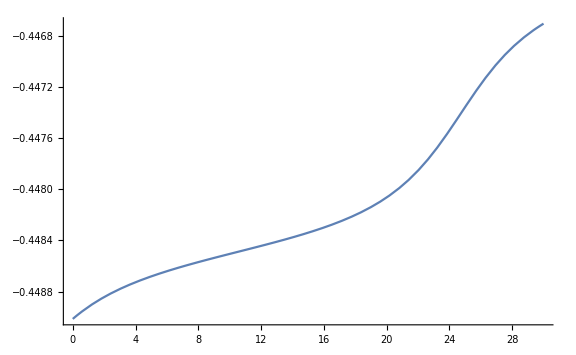
```mathematica
(*p1 =  -Graphics-        ;
p2=Plot[   fcosκ1[T],{T, 00 ,30},PlotStyle->Red];
Show[p2,p1, PlotRange->All, ImageSize->Large]
(*Pause[10000];*)*)
```

# L vector solution

```mathematica
LinitJframe = EulMat.Linit      ;
Lξ10 =   sphericalAngles[LinitJframe][[2]]+ π/2 ;
α1 =-(δ2 (J+Lninit+S2ninit σ2))/(S1ninit (δ1-δ2)) ;
α2 =-(δ2 (-J+Lninit+S2ninit σ2))/(S1ninit (δ1-δ2)) ;
β1 =-1/(2 S1ninit (δ1-δ2))δ2 (Lninit^2 δ1+J^2 δ2+S1ninit (δ1-δ2) (S1ninit+S2ninit σ1)+Lninit S2ninit δ1 σ2+J (Lninit (δ1+δ2)+S2ninit δ2 σ2)) ;
β2 =-1/(2 S1ninit (δ1-δ2))δ2 (Lninit^2 δ1+J^2 δ2+S1ninit (δ1-δ2) (S1ninit+S2ninit σ1)+Lninit S2ninit δ1 σ2-J (Lninit (δ1+δ2)+S2ninit δ2 σ2)) ;
```

```mathematica
solPiece1 =(2/(A(x1-x2))^(1/2)) ((β1  EllipticPi[(x2-x3)/(α1+x2),JacobiAmplitude[Υ,β^2],β^2])/(α1+x2)-(β2 EllipticPi[(x2-x3)/(α2+x2),JacobiAmplitude[Υ,β^2],β^2])/(α2+x2))  ; 
solPiece2 =Lξ10 -(solPiece1/.u2->u0 )    ;
Lξ1sol=solPiece1 + solPiece2  ;
cosκ2[t_]:= σ2 -  δ1 S1ninit/(δ2 S2ninit) fcosκ1[t];
LvecAzimuthAngle[t_]:=-π/2+Lξ1sol/.findu2[t];
LvecPolarAngle[t_]:= ArcCos[(Lninit^2+ Lninit S1ninit  fcosκ1[t] + Lninit S2ninit  cosκ2[t]  )/(Lninit J)]; 
Lsol[t_]:=Module[{Lx,Ly,Lz},
{Lx,Ly,Lz} = vectorComponents[{Lninit, LvecPolarAngle[t],LvecAzimuthAngle[t]}];
Return[ kGoldstein(Inverse[EulMat].{Lx,Ly,Lz}) ]; ];
```

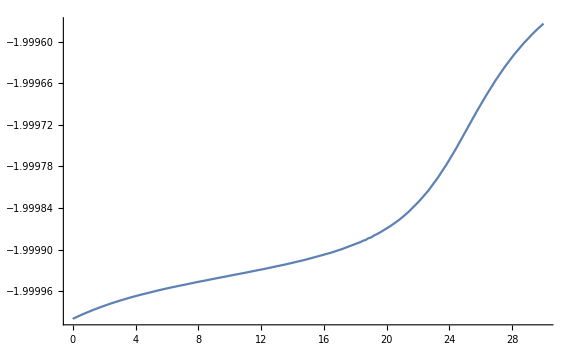
```mathematica
(*p1 = -Graphics-         ;
p2=Plot[Lsol[T][[3]],{T,0,30},PlotStyle->Red, ImageSize->Large];
Show[p1, p2]*)
```

```mathematica
(*Pause[1000];*)
(*Quit[];*)
```

# S1 vector solution

```mathematica
S1initJframe = EulMat.S1init      ;
S1ξ10 =   sphericalAngles[S1initJframe][[2]]+ π/2 ;

α1S1 =  (δ2 (-J+S1ninit+S2ninit σ1))/(Lninit δ1)  ;
α2S1 =(δ2 (J+S1ninit+S2ninit σ1))/(Lninit δ1) ;
β1S1 =-1/(2 Lninit δ1)δ2 (Lninit^2 δ1+(S1ninit (δ1-δ2)+J δ2) (-J+S1ninit+S2ninit σ1)+Lninit S2ninit δ1 σ2)  ;
β2S1 =1/(2 Lninit δ1)δ2 (-Lninit^2 δ1+(-S1ninit δ1+(J+S1ninit) δ2) (J+S1ninit+S2ninit σ1)-Lninit S2ninit δ1 σ2) ;

solPiece1S1 =(2/(A(x1-x2))^(1/2)) ((β1S1  EllipticPi[(x2-x3)/(α1S1+x2),JacobiAmplitude[Υ,β^2],β^2])/(α1S1+x2)-(β2S1 EllipticPi[(x2-x3)/(α2S1+x2),JacobiAmplitude[Υ,β^2],β^2])/(α2S1+x2))   + solPiece0/((n2 G M) ar2^3)  (J δ2)/c^2  ;
solPiece2S1 =S1ξ10 -(solPiece1S1/.u2->u0 )    ;
S1ξ1sol=solPiece1S1 + solPiece2S1  ;

cosγ[t_]:= σ1 +   Lninit(δ1-δ2)/(δ2 S2ninit) fcosκ1[t];
S1vecAzimuthAngle[t_]:=-π/2+S1ξ1sol/.findu2[t];
S1vecPolarAngle[t_]:= ArcCos[(S1ninit^2+ Lninit S1ninit  fcosκ1[t] + S1ninit S2ninit  cosγ[t]  )/(S1ninit J)]; 
S1sol[t_]:=Module[{S1x,S1y,S1z},
{S1x,S1y,S1z} = vectorComponents[{S1ninit, S1vecPolarAngle[t],S1vecAzimuthAngle[t]}];
Return[ spinScalingFactor(Inverse[EulMat].{S1x,S1y,S1z}) ]; ];
S2sol[t_]:=spinScalingFactor(Jvec - Lsol[t]/kGoldstein-S1sol[t]/spinScalingFactor);
```

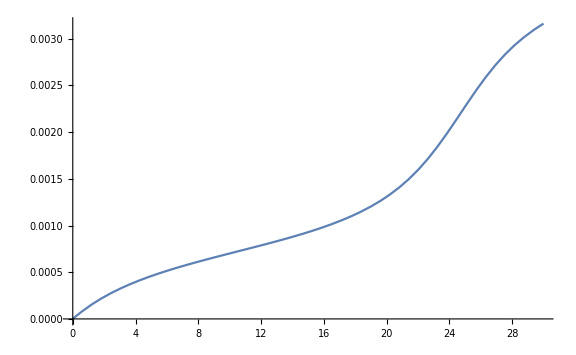
```mathematica
(*p1 =    -Graphics-    ;
p2=Plot[S1sol[T][[1]] ,{T,0,30},PlotStyle->Red, ImageSize->Large];
Show[p1,p2]*)
```

```mathematica
(*Pause[10000] ;*)
```

# R solution

```mathematica
LsolJframe[t_]:=Module[{Lx,Ly,Lz},
{Lx,Ly,Lz} = vectorComponents[{Lninit, LvecPolarAngle[t],LvecAzimuthAngle[t]}];
Return[ kGoldstein({Lx,Ly,Lz}) ]; ];

JtoLframeEulMat[t_]:=Module[{Lx,Ly,Lz, ξ1L, ξ2L},
{Lx,Ly,Lz} = LsolJframe[t];
{ξ2L, ξ1L}=sphericalAngles[{Lx,Ly,Lz}]+{0,π/2};
EulMatJtoL ={ {Cos[ξ1L], Sin[ξ1L],0},{-Sin[ξ1L]Cos[ξ2L], Cos[ξ1L]Cos[ξ2L], Sin[ξ2L]},{Sin[ξ1L]Sin[ξ2L], -Cos[ξ1L]Sin[ξ2L], Cos[ξ2L]}}      ;
Return[EulMatJtoL];];


rinitLframe=JtoLframeEulMat[0].EulMat.rinit       ;
rϕ0 =   sphericalAngles[rinitLframe ][[2]] ;
```

```mathematica
IntReciOfr2 = ((v2 (-1+et2^2-2 ec et2 ϵ))/(√(1-et2^2))+(2 ec ϵ Sin[u2])/(-1+et2 Cos[u2]))/(ar2^2 (-1+et2^2) G M n2)     (*Integral of 1/r^2*)  ;
IntReciOfr3 =((v2 (2-2 et2^2+9 ec et2 ϵ))/(√(1-et2^2))+((2 et2-2 et2^3+6 ec ϵ+3 ec et2^2 ϵ+et2 (-2 et2+2 et2^3-3 ec ϵ-6 ec et2^2 ϵ) Cos[u2]) Sin[u2])/(-1+et2 Cos[u2])^2)/(2 ar2^3 (-1+et2^2)^2 G M n2) (*Integral of 1/r^3*)  ;

IntReciOfr4 =1/(6 ar2^4 G M n2)(-(3 v2 (-2+et2^2+et2^4-16 ec et2 ϵ-4 ec et2^3 ϵ))/((1-et2^2)^(7/2))+(8 ec ϵ Sin[u2])/((-1+et2^2) (-1+et2 Cos[u2])^3)+((3 et2-3 et2^3+8 ec ϵ+12 ec et2^2 ϵ) Sin[u2])/((-1+et2)^2 (1+et2)^2 (-1+et2 Cos[u2])^2)+((9 et2-9 et2^3+8 ec ϵ+52 ec et2^2 ϵ) Sin[u2])/((-1+et2^2)^3 (-1+et2 Cos[u2])))     ;
IntReciOfr5 =   1/(ar2^5 (G M n2))(1/(96 (-1+et2^2)^4)(-(12 v2 (-8-4 et2^2+12 et2^4-100 ec et2 ϵ-75 ec et2^3 ϵ))/(√(1-et2^2))+1/(-1+et2 Cos[u2])^4(288 et2-64 et2^3-136 et2^5-88 et2^7+480 ec ϵ+1920 ec et2^2 ϵ+2620 ec et2^4 ϵ+230 ec et2^6 ϵ+5 et2 (-144 et2+124 et2^3+4 et2^5+16 et2^7-144 ec ϵ-1182 ec et2^2 ϵ-169 ec et2^4 ϵ-80 ec et2^6 ϵ) Cos[u2]+2 et2^2 (152 et2-124 et2^3-28 et2^5+120 ec ϵ+1360 ec et2^2 ϵ+95 ec et2^4 ϵ) Cos[2 u2]-44 et2^4 Cos[3 u2]+28 et2^6 Cos[3 u2]+16 et2^8 Cos[3 u2]-30 ec et2^3 ϵ Cos[3 u2]-415 ec et2^5 ϵ Cos[3 u2]-80 ec et2^7 ϵ Cos[3 u2]) Sin[u2]) )  ;
β1r =  -1/(2 (S1ninit δ1-S1ninit δ2) ϵ)δ2 (-J Lninit δ1 ϵ+Lninit^2 δ1 ϵ+S1ninit^2 δ1 ϵ+J^2 δ2 ϵ-J Lninit δ2 ϵ-S1ninit^2 δ2 ϵ+S1ninit S2ninit δ1 ϵ σ1-S1ninit S2ninit δ2 ϵ σ1+Lninit S2ninit δ1 ϵ σ2-J S2ninit δ2 ϵ σ2);
β2r=-1/(2 (S1ninit δ1-S1ninit δ2) ϵ)δ2 (J Lninit δ1 ϵ+Lninit^2 δ1 ϵ+S1ninit^2 δ1 ϵ+J^2 δ2 ϵ+J Lninit δ2 ϵ-S1ninit^2 δ2 ϵ+S1ninit S2ninit δ1 ϵ σ1-S1ninit S2ninit δ2 ϵ σ1+Lninit S2ninit δ1 ϵ σ2+J S2ninit δ2 ϵ σ2) ;
α1r = (J δ2-Lninit δ2-S2ninit δ2 σ2)/(S1ninit δ1-S1ninit δ2) ;
α2r = (-J δ2-Lninit δ2-S2ninit δ2 σ2)/(S1ninit δ1-S1ninit δ2);
solPiece1r =(2/(A(x1-x2))^(1/2)) ((β1r  EllipticPi[(x2-x3)/(α1r+x2),JacobiAmplitude[Υ,β^2],β^2])/(α1r+x2)+(β2r EllipticPi[(x2-x3)/(α2r+x2),JacobiAmplitude[Υ,β^2],β^2])/(α2r+x2))  ;
solPiece2r =-1/2 IntReciOfr5 Lninit ϵ^2 (-1+3 ν) (2 SeffdLinit+Lninit^2 ν)+1/2 IntReciOfr4 Lninit ϵ^2 (-6+17 ν+3 ν^2)+1/2 IntReciOfr2 Lninit (2-Hinit^2 ϵ^2 (1-3 ν)^2+2 Hinit ϵ (-1+3 ν))-1/Lninit IntReciOfr3 ϵ (-SeffdLinit+Lninit^2 (4+δ1+δ2+4 Hinit ϵ-2 ν-13 Hinit ϵ ν+3 Hinit ϵ ν^2)+Lninit S2ninit δ2 σ2);
solPiece3r =  solPiece1r + solPiece2r ;
```

```mathematica
solPiece4r =rϕ0 -(solPiece3r/.u2->u0 )    ;
rϕsolLframe=solPiece3r + solPiece4r  ;
rvecAzimuthAngleLframe[t_]:=rϕsolLframe/.findu2[t];
rMagnitude[t_] := ar2 (1-er2 Cos[u2])/.findu2[t];
rsol[t_]:=Module[{rx,ry,rz},
{rx,ry,rz} = vectorComponents[{rMagnitude[t], π/2,rvecAzimuthAngleLframe[t]}];
Return[ G M(Inverse[EulMat].Inverse[JtoLframeEulMat[t]].{rx,ry,rz}) ]; ];
```

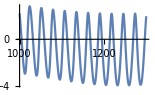
```mathematica
(*p1 =    -Graphics-    ;
p2=Plot[   rsol[t][[1]],{t,1000, 1300},PlotStyle->Red, ImageSize->Large];
Show[p1,p2]*)
```

# P vector solution

```mathematica
pdn[t_] :=  ((2 Hinit + ϵ(1- 3 ν)Hinit^2) + (2(1 + ϵ (4-ν)Hinit))/rMagnitude[t] + (-Lninit^2+ϵ (6+ν))/rMagnitude[t]^2 + (-ϵ ν (Lninit^2+ 2SeffdLinit/ν))/rMagnitude[t]^3  )^(1/2) ;
pMagnitude[t_]:=( pdn[t]^2+Lninit^2/rMagnitude[t]^2)^(1/2) ;
ϕOffsetPvecNIFTemp[t_] :=  ArcSin[Lninit/(rMagnitude[t]pMagnitude[t])] ;
ϕOffsetPvecNIF[t_]:=Module[{tempVar} ,
If[pdn[t] >0,
tempVar = ϕOffsetPvecNIFTemp[t] ,
tempVar = ϕOffsetPvecNIFTemp[t]+2(π/2 - ϕOffsetPvecNIFTemp[t]) ;];
Return[tempVar] ;  ];
pvecAzimuthAngleLframe[t_]:= rvecAzimuthAngleLframe[t]+ϕOffsetPvecNIF[t];
psol[t_]:=Module[{px,py,pz},
{px,py,pz} = vectorComponents[{pMagnitude[t], π/2,pvecAzimuthAngleLframe[t]}];
Return[ μ(Inverse[EulMat].Inverse[JtoLframeEulMat[t]].{px,py,pz}) ]; ];
```

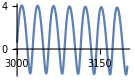
```mathematica
p1 =    -Graphics-    ;
p2=Plot[   rsol[t][[1]],{t,3000,  3200},PlotStyle->Red, ImageSize->Large];
Show[p1,p2]
```

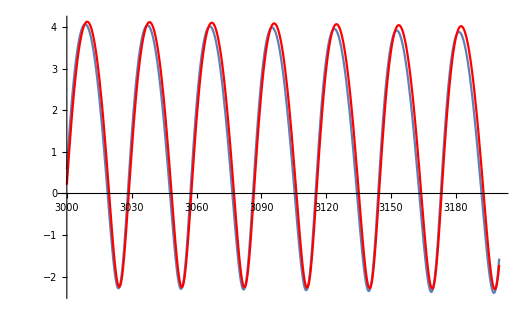

```mathematica
PNparam=G M/ar2 ϵ  //N
(2π)/n2  //N
(2π)/n2         1/PNparam //N
```

0.00877228

29.1158

3319.06